# ComplexMatrixDraw

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

Works on numbers, vectors, and arrays, even with null elements,

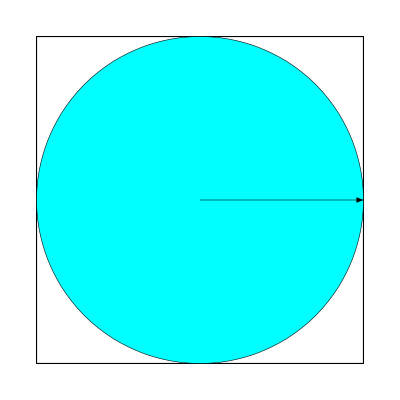
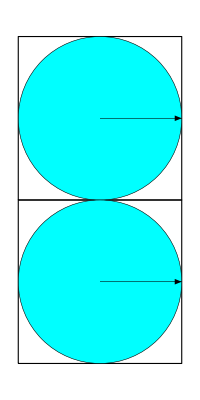
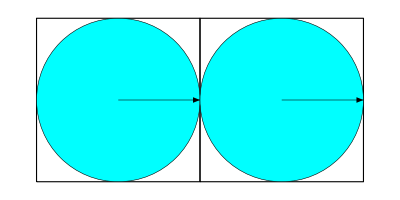
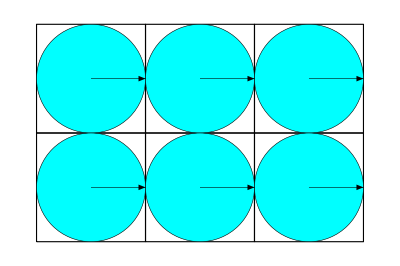
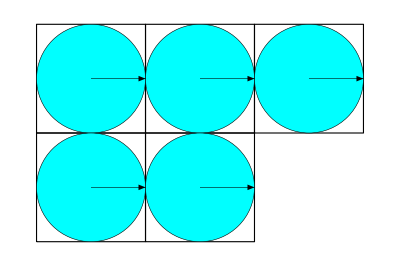
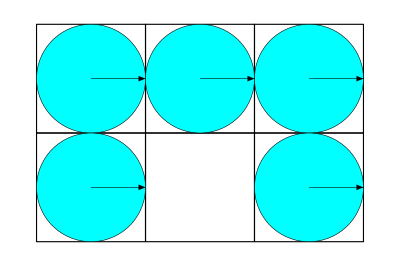

```mathematica
complexMatrixDraw/@ {1,{1,1},{{1,1}},{{1,1,1},{1,1,1}},{{1,1,1},{1,1}},{{1,1,1},{1,,1}}}
```

Test of a few options

```mathematica
Manipulate[Show[complexMatrixDraw[abs Exp[I φ],showFrame->showFrameC,frameFaceFunction->frameFaceFunctionC,showCentralPoint->showCentralPointC,centralPointSize->centralPointSizeC,show2DShape->show2DShapeC,whatShape->whatShapeC,hide2DShapeSmallerThan->hide2DShapeSmallerThanC,borderDirectives->borderDirectivesC,fill2DShape->fill2DShapeC,showArrow->showArrowC,arrowDirectives->arrowDirectivesC,hideArrowSmallerThan->hideArrowSmallerThanC,showLabel->showLabelC,labelShift->labelShiftC,labelStyle->labelStyleC], Frame->True,PlotRange->{{-0.1,1.1},{-0.1,1.1}}],
{{abs,0.5},0,1},{φ,0,2π},
{showFrameC,{True,False},ControlType->Checkbox},
{showCentralPointC,{True,False},ControlType->Checkbox},
 {{centralPointSizeC,0.02},0,0.5},
{{frameFaceFunctionC, {White,Opacity[0]}&}},
{show2DShapeC,{True,False},ControlType->Checkbox},
{whatShapeC,{"circle","square"},ControlType->PopupMenu},
{fill2DShapeC,{True,False},ControlType->Checkbox},
{{borderDirectivesC,{Black,Thickness[0.001]}}},
{{hide2DShapeSmallerThanC,0},0,0.5},
{showArrowC,{True,False},ControlType->Checkbox},
{{arrowDirectivesC,{Black,Thickness[0.005],Arrowheads[0.08]}}},
{{hideArrowSmallerThanC,0},0,0.5},
{showLabelC,{True,False},ControlType->Checkbox},
{{labelShiftC,{0,0.25}},{-0.6,-0.6},{0.6,0.6}},
 {{labelStyleC,Large},{Small,Medium,Large},ControlType->PopupMenu},
 ControlPlacement->Left]
```

Single cell with the  default options and a few additional options

```mathematica
default={};options[1]=default;
options[2]={show2DShape->False};
options[3]={showArrow->False};
options[4]={whatShape->"square"};
options[5]={functionFor2DShapeAera->(Abs[#]^2&)};
options[6]={hideArrowSmallerThan->0.1};
options[7]={fill2DShape->False};
options[8]={frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]] &)};
options[9]={showCentralPoint->True};
options[10]={showLabel->True,labelFunction->((ToString[Round[1000Abs[#]]/10.]<>"%")&), labelStyle->Medium,labelShift->{0,0.3},fill2DShape->False};
optionSets=Table[options[i],{i,10}];
```

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[1] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[2] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[3] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[4] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[5] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[6] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[7] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[8] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[9] is Protected.

Set::write: Tag List in {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)}[10] is Protected.

```mathematica
c=0.499(1+I)/Sqrt[2];
complexMatrixDraw[c,Sequence@@#]&/@optionSets
```

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[0.35284628381208716`  + 0.35284628381208716` ⅈ, {1, -1}, 1]}}].

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[0.35284628381208716`  + 0.35284628381208716` ⅈ, {1, -1}, 2]}}].

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[0.35284628381208716`  + 0.35284628381208716` ⅈ, {1, -1}, 3]}}].

General::stop: Further output of Show will be suppressed during this calculation.

{Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},1]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},2]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},3]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},4]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},5]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},6]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},7]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},8]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},9]}}],Show[{{myPlotElement[0.352846+0.352846 ⅈ,{1,-1},10]}}]}

Rectangular matrix with the  default options and different options

```mathematica
(matrix1={{1,Exp[I π/4],Exp[I π/2],Exp[I 3π/4]},{1,1/2,1/4,1/20},{1,1/2 Exp[I π/4],1/4  Exp[I π/2],1/20Exp[I 3 π/4]}}//Transpose)//MatrixForm
complexMatrixDraw[matrix1,Sequence@@#]&/@optionSets
```

(1 | 1 | 1
ⅇ^((ⅈ π)/4) | 1/2 | 1/2 ⅇ^((ⅈ π)/4)
ⅈ | 1/4 | ⅈ/4
ⅇ^((3 ⅈ π)/4) | 1/20 | 1/20 ⅇ^((3 ⅈ π)/4))

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[1, {1, -1}, 1], myPlotElement[1, {2, -1}, 1], myPlotElement[1, {3, -1}, 1]}, {myPlotElement[ⅇ^ⅈ π/4, {1, -2}, 1], myPlotElement[1/2, {2, -2}, 1], myPlotElement[1/2 ⅇ^ⅈ π/4, {3, -2}, 1]}, {myPlotElement[ⅈ, {1, -3}, 1], myPlotElement[1/4, {2, -3}, 1], myPlotElement[ⅈ/4, {3, -3}, 1]}, {myPlotElement[ⅇ^3 ⅈ π/4, {1, -4}, 1], myPlotElement[1/20, {2, -4}, 1], myPlotElement[1/20 ⅇ^3 ⅈ π/4, {3, -4}, 1]}}].

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[1, {1, -1}, 2], myPlotElement[1, {2, -1}, 2], myPlotElement[1, {3, -1}, 2]}, {myPlotElement[ⅇ^ⅈ π/4, {1, -2}, 2], myPlotElement[1/2, {2, -2}, 2], myPlotElement[1/2 ⅇ^ⅈ π/4, {3, -2}, 2]}, {myPlotElement[ⅈ, {1, -3}, 2], myPlotElement[1/4, {2, -3}, 2], myPlotElement[ⅈ/4, {3, -3}, 2]}, {myPlotElement[ⅇ^3 ⅈ π/4, {1, -4}, 2], myPlotElement[1/20, {2, -4}, 2], myPlotElement[1/20 ⅇ^3 ⅈ π/4, {3, -4}, 2]}}].

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[1, {1, -1}, 3], myPlotElement[1, {2, -1}, 3], myPlotElement[1, {3, -1}, 3]}, {myPlotElement[ⅇ^ⅈ π/4, {1, -2}, 3], myPlotElement[1/2, {2, -2}, 3], myPlotElement[1/2 ⅇ^ⅈ π/4, {3, -2}, 3]}, {myPlotElement[ⅈ, {1, -3}, 3], myPlotElement[1/4, {2, -3}, 3], myPlotElement[ⅈ/4, {3, -3}, 3]}, {myPlotElement[ⅇ^3 ⅈ π/4, {1, -4}, 3], myPlotElement[1/20, {2, -4}, 3], myPlotElement[1/20 ⅇ^3 ⅈ π/4, {3, -4}, 3]}}].

General::stop: Further output of Show will be suppressed during this calculation.

{Show[{{myPlotElement[1,{1,-1},1],myPlotElement[1,{2,-1},1],myPlotElement[1,{3,-1},1]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},1],myPlotElement[1/2,{2,-2},1],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},1]},{myPlotElement[ⅈ,{1,-3},1],myPlotElement[1/4,{2,-3},1],myPlotElement[ⅈ/4,{3,-3},1]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},1],myPlotElement[1/20,{2,-4},1],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},1]}}],Show[{{myPlotElement[1,{1,-1},2],myPlotElement[1,{2,-1},2],myPlotElement[1,{3,-1},2]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},2],myPlotElement[1/2,{2,-2},2],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},2]},{myPlotElement[ⅈ,{1,-3},2],myPlotElement[1/4,{2,-3},2],myPlotElement[ⅈ/4,{3,-3},2]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},2],myPlotElement[1/20,{2,-4},2],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},2]}}],Show[{{myPlotElement[1,{1,-1},3],myPlotElement[1,{2,-1},3],myPlotElement[1,{3,-1},3]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},3],myPlotElement[1/2,{2,-2},3],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},3]},{myPlotElement[ⅈ,{1,-3},3],myPlotElement[1/4,{2,-3},3],myPlotElement[ⅈ/4,{3,-3},3]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},3],myPlotElement[1/20,{2,-4},3],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},3]}}],Show[{{myPlotElement[1,{1,-1},4],myPlotElement[1,{2,-1},4],myPlotElement[1,{3,-1},4]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},4],myPlotElement[1/2,{2,-2},4],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},4]},{myPlotElement[ⅈ,{1,-3},4],myPlotElement[1/4,{2,-3},4],myPlotElement[ⅈ/4,{3,-3},4]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},4],myPlotElement[1/20,{2,-4},4],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},4]}}],Show[{{myPlotElement[1,{1,-1},5],myPlotElement[1,{2,-1},5],myPlotElement[1,{3,-1},5]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},5],myPlotElement[1/2,{2,-2},5],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},5]},{myPlotElement[ⅈ,{1,-3},5],myPlotElement[1/4,{2,-3},5],myPlotElement[ⅈ/4,{3,-3},5]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},5],myPlotElement[1/20,{2,-4},5],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},5]}}],Show[{{myPlotElement[1,{1,-1},6],myPlotElement[1,{2,-1},6],myPlotElement[1,{3,-1},6]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},6],myPlotElement[1/2,{2,-2},6],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},6]},{myPlotElement[ⅈ,{1,-3},6],myPlotElement[1/4,{2,-3},6],myPlotElement[ⅈ/4,{3,-3},6]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},6],myPlotElement[1/20,{2,-4},6],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},6]}}],Show[{{myPlotElement[1,{1,-1},7],myPlotElement[1,{2,-1},7],myPlotElement[1,{3,-1},7]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},7],myPlotElement[1/2,{2,-2},7],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},7]},{myPlotElement[ⅈ,{1,-3},7],myPlotElement[1/4,{2,-3},7],myPlotElement[ⅈ/4,{3,-3},7]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},7],myPlotElement[1/20,{2,-4},7],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},7]}}],Show[{{myPlotElement[1,{1,-1},8],myPlotElement[1,{2,-1},8],myPlotElement[1,{3,-1},8]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},8],myPlotElement[1/2,{2,-2},8],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},8]},{myPlotElement[ⅈ,{1,-3},8],myPlotElement[1/4,{2,-3},8],myPlotElement[ⅈ/4,{3,-3},8]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},8],myPlotElement[1/20,{2,-4},8],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},8]}}],Show[{{myPlotElement[1,{1,-1},9],myPlotElement[1,{2,-1},9],myPlotElement[1,{3,-1},9]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},9],myPlotElement[1/2,{2,-2},9],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},9]},{myPlotElement[ⅈ,{1,-3},9],myPlotElement[1/4,{2,-3},9],myPlotElement[ⅈ/4,{3,-3},9]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},9],myPlotElement[1/20,{2,-4},9],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},9]}}],Show[{{myPlotElement[1,{1,-1},10],myPlotElement[1,{2,-1},10],myPlotElement[1,{3,-1},10]},{myPlotElement[ⅇ^((ⅈ π)/4),{1,-2},10],myPlotElement[1/2,{2,-2},10],myPlotElement[1/2 ⅇ^((ⅈ π)/4),{3,-2},10]},{myPlotElement[ⅈ,{1,-3},10],myPlotElement[1/4,{2,-3},10],myPlotElement[ⅈ/4,{3,-3},10]},{myPlotElement[ⅇ^((3 ⅈ π)/4),{1,-4},10],myPlotElement[1/20,{2,-4},10],myPlotElement[1/20 ⅇ^((3 ⅈ π)/4),{3,-4},10]}}]}

Comparison of two matrices

```mathematica
gr1=complexMatrixDraw[matrix1,Sequence@@#]&/@(Join[{borderDirectives->{Blue},arrowDirectives->{Blue},fill2DShape->False},#]&/@optionSets);(matrix2=Map[(1-RandomReal[{0.1,0.2}])Exp[I RandomReal[{-π/10.,π/10}]]#&, matrix1,{2}])//MatrixForm;
gr2=complexMatrixDraw[matrix2,Sequence@@#]&/@(Join[{borderDirectives->{Thickness[.001],Red},arrowDirectives->{Thickness[.001],Red},fill2DShape->False,labelShift->{0,-0.3}},#]&/@optionSets);
MapThread[Show[{#1,#2}]&,{gr1,gr2}]
```

Join::heads: Heads List and {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)} at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[1, {1, -1}, {borderDirectives → {RGBColor[« 3 »]}, arrowDirectives → {RGBColor[« 3 »]}, fill2DShape → False}, {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[1]], myPlotElement[1, {2, -1}, « 1 », {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[1]], myPlotElement[1, {3, -1}, {borderDirectives → {RGBColor[« 3 »]}, arrowDirectives → {RGBColor[« 3 »]}, fill2DShape → False}, {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[1]]}, {« 1 »}, {« 1 »}, « 1 »}].

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[1, {1, -1}, {borderDirectives → {RGBColor[« 3 »]}, arrowDirectives → {RGBColor[« 3 »]}, fill2DShape → False}, {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[2]], myPlotElement[1, {2, -1}, « 1 », {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[2]], myPlotElement[1, {3, -1}, {borderDirectives → {RGBColor[« 3 »]}, arrowDirectives → {RGBColor[« 3 »]}, fill2DShape → False}, {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[2]]}, {« 1 »}, {« 1 »}, « 1 »}].

Show::gcomb: Could not combine the graphics objects in Show[{{myPlotElement[1, {1, -1}, {borderDirectives → {RGBColor[« 3 »]}, arrowDirectives → {RGBColor[« 3 »]}, fill2DShape → False}, {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[3]], myPlotElement[1, {2, -1}, « 1 », {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[3]], myPlotElement[1, {3, -1}, {borderDirectives → {RGBColor[« 3 »]}, arrowDirectives → {RGBColor[« 3 »]}, fill2DShape → False}, {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[« 1 »], RGBColor[« 3 »]}, fill2DShape → True, borderDirectives → {Thickness[« 1 »], GrayLevel[« 1 »]}, fillingColor → (RGBColor[« 3 »] &)}[3]]}, {« 1 »}, {« 1 »}, « 1 »}].

General::stop: Further output of Show will be suppressed during this calculation.

Join::heads: Heads List and {hideArrowSmallerThan → 0.1`, arrowDirectives → {Thickness[0.0001`], RGBColor[1, 0, 0]}, fill2DShape → True, borderDirectives → {Thickness[0.0001`], GrayLevel[0]}, fillingColor → (RGBColor[#2/Times[« 2 »] + 0.5`, 0.5`  + #2/Times[« 2 »], 0.5`  - Slot[« 1 »] Power[« 2 »]] &)} at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{« 1 »}].

General::stop: Further output of Show will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{Show[« 1 »], Show[{« 1 »}]}].

General::stop: Further output of Show will be suppressed during this calculation.

{«1»}

## My Code

```mathematica
replacements={"j"->"ⅈ","e"->"*10^"};
myImport[fileName_,type_,headerLines_:0,printHeader_:False]:=
Block[
{data=Import[fileName,type],l},
If[printHeader,Print["Header: "<>ToString[Take[data,headerLines]]]];
data=(Map[StringReplace[#,replacements]&,Drop[data,headerLines],{2}])// ToExpression//Chop;
data=data//Partition[#,2]&//Transpose;
l=ToString[Length[data[[1]]]];
"{{"<>l<>" ρIn},{"<>l<>" ρOut}}" //Print;
data
]
{inputDensityMatrices,outputDensityMatrices}=myImport["P:\\local-expdata\\FO-C5\\3rd-Run\\2011_04_21\\good_data\\Quantum Process Tomography at 31 ns-3-density matrices-2.txt","Table",1,True];
```

Header: {{0, 1, 2, 3, 10, 11, 12, 13, 20, 21, 22, 23, 30, 31, 32, 33}}

{{16 ρIn},{16 ρOut}}

```mathematica
inputDensityMatrices[[3,15]]
```

-0.0398877-0.0341716 ⅈ

```mathematica
k = 5
options = {hideArrowSmallerThan->0.1,arrowDirectives->{Thickness[.0001],Red},fill2DShape->True,borderDirectives->{Thickness[.0001],Black},fillingColor->(RGBColor[#2/(2π)+0.5,0.5+#2/(2π),0.5-#2/(2π)]&)}
rhoInput = Table[inputDensityMatrices[[k,(i-1)*4+j]],{i,1,4},{j,1,4}];
rhoOutput = Table[outputDensityMatrices[[k,(i-1)*4+j]],{i,1,4},{j,1,4}];
complexMatrixDraw[rhoInput,options]
complexMatrixDraw[rhoOutput,options]
```

5

{hideArrowSmallerThan→0.1,arrowDirectives→{Thickness[0.0001],RGBColor[1,0,0]},fill2DShape→True,borderDirectives→{Thickness[0.0001],GrayLevel[0]},fillingColor→(RGBColor[#2/(2 π)+0.5,0.5+#2/(2 π),0.5-#2/(2 π)]&)}

complexMatrixDraw[{{0.0425776,0.147564-0.0663089 ⅈ,0.00484018-0.00370742 ⅈ,-0.00965811-0.0182363 ⅈ},{0.147564+0.0663089 ⅈ,0.915966,0.0176585-0.0135162 ⅈ,-0.0452807-0.037537 ⅈ},{0.00484018+0.00370742 ⅈ,0.0176585+0.0135162 ⅈ,-0.000379411,-0.00532275+0.00770713 ⅈ},{-0.00965811+0.0182363 ⅈ,-0.0452807+0.037537 ⅈ,-0.00532275-0.00770713 ⅈ,0.0418362}},{hideArrowSmallerThan→0.1,arrowDirectives→{Thickness[0.0001],RGBColor[1,0,0]},fill2DShape→True,borderDirectives→{Thickness[0.0001],GrayLevel[0]},fillingColor→(RGBColor[#2/(2 π)+0.5,0.5+#2/(2 π),0.5-#2/(2 π)]&)}]

complexMatrixDraw[{{0.116038,0.0585802+0.00646611 ⅈ,-0.00602633+0.0901142 ⅈ,0.0192864-0.0170619 ⅈ},{0.0585802-0.00646611 ⅈ,0.374694,-0.00544618+0.448414 ⅈ,-0.0218998-0.0429235 ⅈ},{-0.00602633-0.0901142 ⅈ,-0.00544618-0.448414 ⅈ,0.465839,-0.0526098+0.0242779 ⅈ},{0.0192864+0.0170619 ⅈ,-0.0218998+0.0429235 ⅈ,-0.0526098-0.0242779 ⅈ,0.0434293}},{hideArrowSmallerThan→0.1,arrowDirectives→{Thickness[0.0001],RGBColor[1,0,0]},fill2DShape→True,borderDirectives→{Thickness[0.0001],GrayLevel[0]},fillingColor→(RGBColor[#2/(2 π)+0.5,0.5+#2/(2 π),0.5-#2/(2 π)]&)}]

```mathematica
densityMatrices[[2]]
```

Part::partd: Part specification densityMatrices ⟦ 2 ⟧ is longer than depth of object.

densityMatrices⟦2⟧

```mathematica
Tr[rho]
```

Tr[rho]

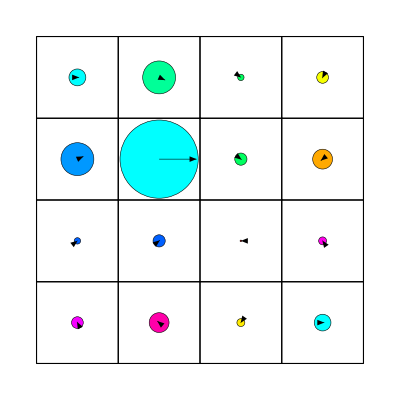

```mathematica
complexMatrixDraw[rhoInput]
```

```mathematica
BarChart3D[Abs[rhoInput],ChartLayout->"Grid",ChartStyle->{{Red,Green,Blue,Brown,Yellow,Magenta,Green,Yellow}}]
```

-Graphics3D-

```mathematica
Abs[rhoInput]
```

{{0.0425776,0.161778,0.00609691,0.0206359},{0.161778,0.915966,0.0222375,0.0588164},{0.00609691,0.0222375,0.000379411,0.00936651},{0.0206359,0.0588164,0.00936651,0.0418362}}